#### Phase estimation

How many photons do we need to estimate phase?

```mathematica
numPhotons=100.;
phaseError=1/√numPhotons
phaseErrorDegrees=180/π phaseError
fid=1-1/4 phaseError^2
```

Here is why:

```mathematica
state=Transpose[{{0,1/√2,1/√2,0}}];
statePhase=Transpose[{{0,1/√2,Exp[ⅈ θ]/√2,0}}];

ρ=state.state†;
ρPhase=statePhase.statePhase†;
```

```mathematica
Fidelity[a_,b_]:=(Plus@@(Sqrt[Eigenvalues[a.b]]))^2;
```

```mathematica
FullSimplify[ComplexExpand[Fidelity[ρ,ρPhase]]]
```

Cos[θ/2]^2

```mathematica
FullSimplify[ComplexExpand[(Abs[(state†.statePhase)][[1,1]])^2]]
```

Cos[θ/2]^2

```mathematica
Integrate[Cos[θ/2]^2 Exp[-1/2 (θ/σ)^2]/(σ √(2 π))/.σ->0.25,{θ,-∞,∞}]
```

0.984617+0. ⅈ

0.1

5.72958

0.9975

At least 100 photons would be good. So about 100 mus to estimate phase after a click.

#### Estimator

Just cus I feel like idiot checking that even a simple estimator can saturate the bound:

```mathematica
out1PhotonNumber=n Cos[θ/2]^2;
out2PhotonNumber=n Sin[θ/2]^2;
```

```mathematica
thetaEst=ArcCos[(out1-out2)/(out1+out2)];
```

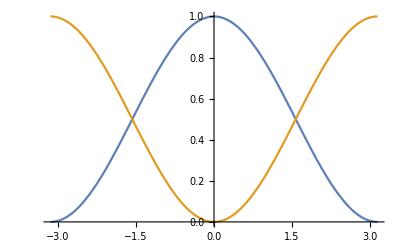

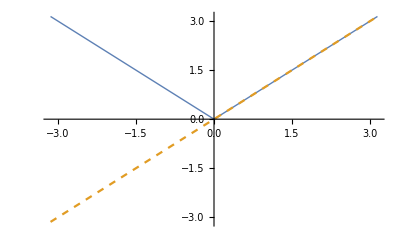

```mathematica
Plot[Evaluate[{out1PhotonNumber,out2PhotonNumber}/.n->1],{θ,-π,π}]
Plot[{thetaEst/.{out1->out1PhotonNumber,out2->out2PhotonNumber},θ},{θ,-π,π},PlotStyle->{Thick,Dashed}]
```

```mathematica
error=FullSimplify[(√((FullSimplify@D[thetaEst,out1])^2 out1+(FullSimplify@D[thetaEst,out2])^2 out2))/.{out1->out1PhotonNumber,out2->out2PhotonNumber}]
```

√(1/n)

Hmmm, its gonna be tricky with the phase wrapping. See e.g. these measurements, where from 10-15 it would be ambiguous what the phase is...

#### Implementation

Current parameters:

Measured 100000 photons per s when illuminating one side with 16 nW

```mathematica
PhaseEstimCountsPerSPernW=1*^5/16.;
```

50 ns dead time for apd. So probably shouldn’t have much more than one or two photons per μs. 

How much power do we need for this?

```mathematica
nWsToSaturateAPDs=(1/1*^-6)/(PhaseEstimCountsPerSPernW)
```

160.